## Import Raw Data

```mathematica
rawCoordinates = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

## List of distances

### Import pair name data

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
flatPairNames=Flatten[PairNames];
```

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

```mathematica
currentPairData=Import[FileNameJoin[{dataDirectory,flatPairNames[[1]]}]];
```

### Implement for one pair

Make a list for each pair that has True or False if they are associated for each time step.
- Split at each point where the larger threshold is crossed
- lists that contain values below the smaller threshold are considered connected
- Join back and make clusters, omitting missing sheep

Split behind each Indeterminate group
Split groups based on below or above 50
Rejoin inner layer

```mathematica
testSplit=Catenate/@Split[Split[currentPairData,( #1≤50&&#2≤50||#1>50&&#2>50||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]50&&second\[VectorLessEqual]50||first\[VectorGreater]50 &&second\[VectorGreater]50]&];
```

```mathematica
testListResult=MemberQ[#,_?(Function[x,x<30])]&/@testSplit;
```

```mathematica
testFinalAssociation=Catenate[MapIndexed[Table[testListResult[[First[#2]]],Length[#1]]&,testSplit]];
```

### Turn into function

```mathematica
determineConnections[pair_,{r1_,r2_}]:=
Module[{split,testList,final},
split=
Catenate/@Split[Split[pair,( #1≤r2&&#2≤r2||#1>r2&&#2>r2||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]r2&&second\[VectorLessEqual]r2||first\[VectorGreater]r2 &&second\[VectorGreater]r2]&];
testList=MemberQ[#,_?(Function[x,x<r1])]&/@split;
final =Catenate[MapIndexed[Table[testList[[First[#2]]],Length[#1]]&,split]]
]
```

## Run it on everything

```mathematica
allPairData=Map[Import[FileNameJoin[{dataDirectory,#}]]&,PairNames,{2}];
```

```mathematica
allPairData[[1]]
```

{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,210335,110.679,110.88,112.892,118.282,122.057,124.546,125.826,Indeterminate},48,{1}}
 |  |  |  |

```mathematica
allPairData[[2]]
```

{{Indeterminate,8.98968,7.70548,6.77705,10.2766,13.4664,Indeterminate,Indeterminate,210335,9.05982,7.63821,7.88773,7.88773,7.88773,7.88773,6.97599,Indeterminate},48}
 |  |  |  |

### Run on 100 time steps

```mathematica
MostPairData=allPairData[[All,All,700;;800]];
```

Run on just the 100 time steps

```mathematica
testcons=Transpose[Catenate[Map[determineConnections[#,{30,50}]&,MostPairData,{2}]]];
```

Generate all possible edges

```mathematica
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,PairNames,{2}]];
```

Show the first 5 networks that were generated

## New draft

```mathematica
symmetricalStickyDBSCAN[data_,{r1_,r2_},{tmin_,tmax_},rawCoordinates_]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,data,{2}]];

MapIndexed[
With[{members=Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{__?NumericQ},{1},Heads->False]]},
ConnectedComponents[Graph[
(*pick vertexes*)
members,
(*pick connections*)
Select[Pick[allEdges,#1,True],FreeQ[Alternatives@@Complement[Range[Length[data]],members]]]]]]&,cons]]
```

```mathematica
symmetricalStickyDBSCAN[allPairData,{30,50},{700,703},rawCoordinates]
```

{{{23,4,5,13,29,35,44,45,6,46},{2,1,10,11,17,22,27,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{28},{14},{26},{31}},{{23,4,5,13,29,35,44,45,6,46},{2,1,10,11,17,22,27,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{28},{14},{26},{31}},{{23,4,5,13,29,35,44,45,6,46},{2,1,10,11,17,22,27,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{28},{14},{26},{31}},{{23,4,5,13,29,35,44,45,6,46},{2,1,10,11,17,22,27,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{28},{14},{26},{31}}}

```mathematica
DBSCAN30Sticky50LonelySheep=symmetricalStickyDBSCAN[allPairData,{30,50},{1,210351},rawCoordinates];
```

```mathematica
EmitSound[SoundNote[]]
```

## Tests

```mathematica
testData[testdist_]:=MapThread[Transpose[{##}]&,Function[{ps},MapIndexed[#1[[#2[[1]]+1;;]]&,DistanceMatrix[ps]]//N]/@testdist]
```

```mathematica
testcoordsFromDist[testdist_]:=List/@#&/@Transpose[testdist]
```

```mathematica
testDistDBSCAN[testdist_]:=symmetricalStickyDBSCAN[testData[testdist],{30,50},{1,Length[testdist]},testcoordsFromDist[testdist]]//Column
```

#### Expectation: sheep 4 moves from one group to the other group

```mathematica
testdistOneSheepMoves={{1,70,2,60},{2,80,3,6},{2,85,4,8}};
```

```mathematica
testDistDBSCAN[testdistOneSheepMoves]
```

{{1,3},{2,4}}
{{1,3,4},{2}}
{{1,3,4},{2}}

#### Expectation: Apart for the first 3 steps, together for 2, apart for 2

```mathematica
testdistInlargerRadius = {{1,40},{2,40},{2,70},{2,40},{1,20},{1,80},{2,50}};
```

```mathematica
testDistDBSCAN[testdistInlargerRadius]
```

{{1},{2}}
{{1},{2}}
{{1},{2}}
{{1,2}}
{{1,2}}
{{1},{2}}
{{1},{2}}

#### Expectation: One group for 2 steps, two groups for 2 steps

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,100},{1,35,70}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{2,1},{3}}
{{2,1},{3}}

#### Expectation: Together the first 4 steps, then apart for 1

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,Missing[]},{1,35,70},{1,70,Missing[]}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,3},{2}}

```mathematica
allEdges[[1]]===UndirectedEdge[1,2]
```

True

## Plot Results

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]*10,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],2]]]]}&/@VertexList[g]),Frame->True,FrameTicks->True(*Echo@{{Automatic,FindDivisions[MinMax[VertexList[g][[All,-1]]]*10,6]},{Automatic,Automatic}}*),EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Medium],Style["Average y-coordinate of the sheep",Medium]}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep];
```

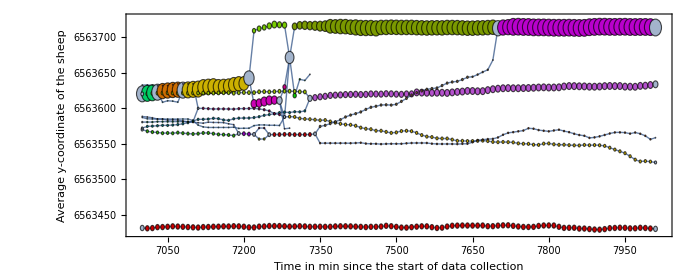

```mathematica
coloredGraph[graph30Sticky50,50]
```

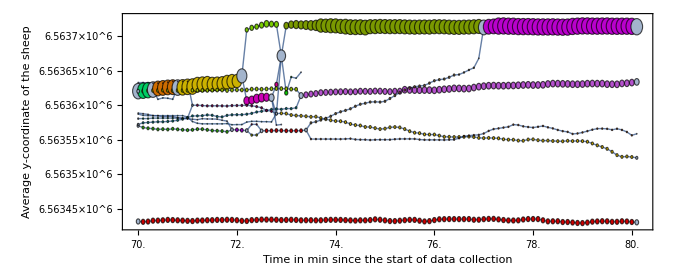

```mathematica
Show[%427,FrameTicks->ReplacePart[ MapAt[If[#[[2]]==="",#,ReplacePart[#,2->#[[1]]/100]]&,AbsoluteOptions[%427,FrameTicks][[1,2]],{1,All}],{{3},{4}}->None]]
```

```mathematica
DBSCAN30Sticky50LonelySheep[[;;2]]
```

{{{38,5,8,17,21,22,33,35,40,44,48},{15},{16},{25},{7},{28},{34},{29},{39},{20},{37},{50},{9},{43},{46},{32},{41},{4},{51},{13},{19},{27},{30},{3},{42},{45},{11},{14},{26},{47},{10},{12},{49},{18},{24},{36},{31},{1},{2},{6},{23}},{{38,2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,39,40,41,42,44,45,46,47,48,51},{15},{28},{50},{43},{32},{13},{30},{49},{1},{6}}}